```mathematica
Complex Expand Command
```

Command Complex Expand

```mathematica
ComplexExpand[(x+I y)^3]
```

x^3-3 x y^2+ⅈ (3 x^2 y-y^3)

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
ComplexExpand[Sin[x+I y]^3]
```

Cosh[y]^3 Sin[x]^3-3 Cos[x]^2 Cosh[y] Sin[x] Sinh[y]^2+ⅈ (3 Cos[x] Cosh[y]^2 Sin[x]^2 Sinh[y]-Cos[x]^3 Sinh[y]^3)

```mathematica
ComplexExpand[12/(√3+I)]
```

-3 ⅈ+3 √3

```mathematica
ComplexExpand[(1+I)(√3+I)]
```

-1+√3+ⅈ (1+√3)

```mathematica
ComplexExpand[{(2+I)(2-I)^2/(1+2I)^2,((√3-I)^2(1+I)^2)/(√3+I)^2}]
```

{-2-ⅈ,-ⅈ+√3}

## Plot the following regions 1. |z|<1 2. 4<|z|<8 3. Absolute(x+iy),x>1 4. Re(z)<2, Img(z)<3 5. Absolute[(z-1)/(z+1)>=2 6. zz̄=1 7. |z|=1 8. |z-(1+i)|=1

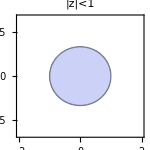
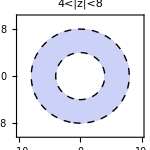
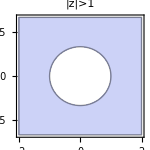
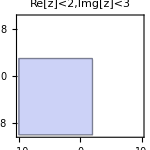
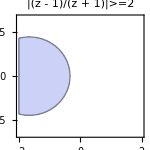

```mathematica
z=x+I y;
A1=RegionPlot[Abs[z]<1,{x,-2,2},{y,-2,2},ImageSize->150,PlotLabel->"|z|<1"];
A2=RegionPlot[4<Abs[z]<8,{x,-10,10},{y,-10,10},ImageSize->150,
BoundaryStyle->Dashed,PlotLabel->"4<|z|<8"];
A3=RegionPlot[Abs[x+I*y]>1,{x,-2,2},{y,-2,2},ImageSize->150,
PlotLabel->"|z|>1"];
A4=RegionPlot[Re[z]<2&&Im[z]<3,{x,-10,10},{y,-10,10},ImageSize->150,
PlotLabel->"Re[z]<2,Img[z]<3"];
A5=RegionPlot[Abs[(z-1)/(z+1)]≥2,{x,-2,2},{y,-2,2},ImageSize->150,
PlotLabel->"|(z - 1)/(z + 1)|>=2"];
Print[A1,A2,A3,A4,A5]
A6=ContourPlot[z*Conjugate[z]-1==1,{x,-2,2},{y,-2,2},Axes->True,ImageSize->150,PlotLabel->"zz̄=1"];
A7=ContourPlot[Abs[z]==1,{x,-2,2},{y,-2,2},Axes->True,ImageSize->150,PlotLabel->"|z|=1"];
```

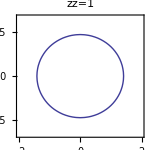
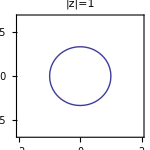

```mathematica
Print[A6,A7]
```

Line joining any two complex numbers

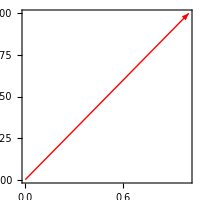

```mathematica
z1=Input["Enter first complex number"];
z2=Input["Enter second complex number"];
Graphics[{Thick,Red,Arrow[{{{Re[z1],Im[z1]},{Re[z2],Im[z2]}}}]},Axes->True,ImageSize->200,Frame->True]
```

# PEACTICAL 1

Make a geometrical plot to show that nth roots of unity are equally spaced points that lie on the unit circle C_1(0)={z:|z|=1} and form the vertices of a regular polygon with n sides for n=4,5,6,7,8.

For n=4

```mathematica
ComplexExpand[z/.Solve[z^4-1==0]]
```

{-1,-ⅈ,ⅈ,1}

```mathematica
A1=Show[Graphics[{Thick,Red,Circle[{0,0},1]}],
ListLinePlot[{{-1,0},{0,-1},{1,0},{0,1},{-1,0}},
PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,
ImageSize->100,PlotLabel->"For n=4"];
```

```mathematica
ComplexExpand[z/.N[Solve[z^5-1==0]]]
```

{1.,-0.809017-0.587785 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ}

```mathematica
A2=Show[Graphics[{Thick,Blue,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1,0}},
PlotStyle->{Purple,Dashed,Thick},PlotMarkers->Automatic],Axes->True,
ImageSize->100,PlotLabel->"For n=5"];
```

```mathematica
ComplexExpand[z/.N[Solve[z^6-1==0]]]
```

{-1.,1.,-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

```mathematica
A3=Show[Graphics[{Thick,Blue,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.5,0.866025},{-0.5,0.8662025},{-1,0},{-0.5,-0.866025},{0.5,-0.866025},{1,0}},
PlotStyle->Green,PlotMarkers->Automatic],Axes->True,
ImageSize->100,PlotLabel->"For n=6"];
```

```mathematica
ComplexExpand[z/.N[Solve[z^7-1==0]]]
```

{1.,-0.900969-0.433884 ⅈ,0.62349+0.781831 ⅈ,-0.222521-0.974928 ⅈ,-0.222521+0.974928 ⅈ,0.62349-0.781831 ⅈ,-0.900969+0.433884 ⅈ}

```mathematica
A4=Show[Graphics[{Thick,Blue,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831},{1,0}},
PlotStyle->{Purple,Dashed,Thick},PlotMarkers->Automatic],Axes->True,
ImageSize->100,PlotLabel->"For n=7"];
```

```mathematica
ComplexExpand[z/.N[Solve[z^8-1==0]]]
```

{-1.,0.-1. ⅈ,0.+1. ⅈ,1.,-0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ}

```mathematica
A5=Show[Graphics[{Thick,Blue,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.707107,0.707107},{0,1},{-0.707107,0.707107},{-1,0},{-0.707107,-0.707107},{0,-1},{0.707107,-0.707107},{1,0}},
PlotStyle->{Purple,Dashed,Thick},PlotMarkers->Automatic],Axes->True,
ImageSize->100,PlotLabel->"For n=8"];
```

```mathematica
Print[A1,A2,A3,A4,A5]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

# PRACTICAL 2

Find the solutions of the equation z^3=8i and represent these geometrically.

```mathematica
Quit[]
```

```mathematica
pts=ComplexExpand[z/.Solve[z^3-8*I==0]]
```

{-2 ⅈ,ⅈ-√3,ⅈ+√3}

ComplexListPlot[{{-2 ⅈ,ⅈ-√3,ⅈ+√3}},PlotStyle→{RGBColor[1,0,0],Thickness[3.5]},PlotMarkers→Automatic,ImageSize→250]

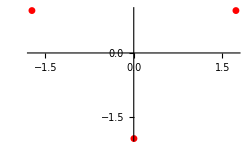

```mathematica
ListPlot[{{0,-2},{-√3,1},{√3,1}},
PlotStyle->{Red,Thickness[3.5]},PlotMarkers->Automatic,
ImageSize->250]
```

# PRACTICAL 3

Write parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units. Show the effect of rotation of this ellipse by an angle of π/6  radians and shifting of the centre from (0,0) to (2,1) by making a parametric plot.

Ellipse:x^2/16+y^2/4=1
The parametric equation is: x=4Cost, y=2Sint: t[0,2Pi]

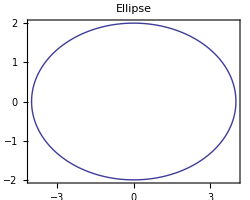

```mathematica
A1=ParametricPlot[{4Cos[t],2Sin[t]},{t,0,2Pi},Frame->True, ImageSize->250, PlotLabel->"Ellipse"];
Print[A1]
```

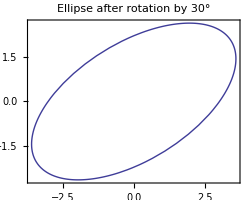

```mathematica
A2=ParametricPlot[{4Cos[t]Cos[π/6]-2Sin[t]Sin[π/6],4Cos[t]Sin[π/6]+2Sin[t]Cos[π/6]},{t,0,2Pi},Frame->True, ImageSize->250, PlotLabel->"Ellipse after rotation by 30°"];
Print[A2]
```

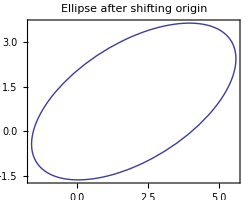

```mathematica
A3=ParametricPlot[{4Cos[t]Cos[π/6]-2Sin[t]Sin[π/6]+2,4Cos[t]Sin[π/6]+2Sin[t]Cos[π/6]+1},{t,0,2Pi},Frame->True, ImageSize->250, PlotLabel->"Ellipse after shifting origin"];
Print[A3]
```

# PRACTICAL-4

Find the image of D1={z:|z+1+i|<1} under the mapping f(z)=(3-4i)z+6+2i

```mathematica
Solve[w1==(3-4I)z1+(6+2I),z1]
```

{{z1→1/25 (-10+3 w1+2 ⅈ (-15+2 w1))}}

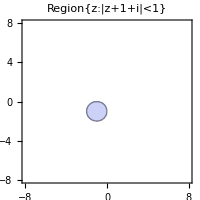
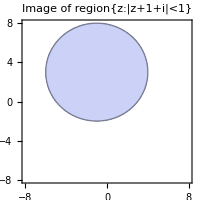

```mathematica
z=x+I y;
A1=RegionPlot[Abs[z+(1+I)]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->200,
PlotLabel->"Region{z:|z+1+i|<1}"];
A2=RegionPlot[Abs[1/25(-10+3z+2I(-15+2z))+1+I]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->200,
PlotLabel->"Image of region{z:|z+1+i|<1}"];
Print[A1,A2]
```

Find the image of the semi-disc S={z:|z|<1, Im z>0} under the mapping f(z)=1/(z+1)

```mathematica
Solve[w1==1/(Subscript[z, 1]+1),Subscript[z, 1]]
```

{{(x+ⅈ y)_1→(1-w1)/w1}}

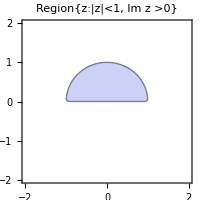
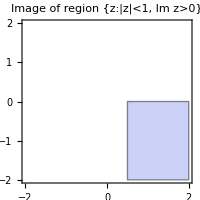

```mathematica
A1=RegionPlot[Abs[z]<1&& Im[z]>0,{x,-2,2},{y,-2,2},Axes->True,ImageSize->200,
PlotLabel->"Region{z:|z|<1, Im z >0}"];
A2=RegionPlot[Abs[1/z-1]<1&& Im[1/z-1]>0,{x,-2,2},{y,-2,2},Axes->True,ImageSize->200,
PlotLabel->"Image of region {z:|z|<1, Im z>0}"];
Print[A1,A2]
```

# PRACTICAL-5

Show that image of D_1 ={z:Re(z)>1} under the mapping f(z)=(-1+i)z-2+3i is the half plane v>u+7, where u=Re(w) etc. Plot the map.

```mathematica
Solve[w1==(-1+I)Subscript[z, 1]-2+3I,Subscript[z, 1]]
```

{{(x+ⅈ y)_1→1/2 (-5+ⅈ (1-w1)-w1)}}

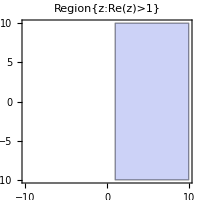
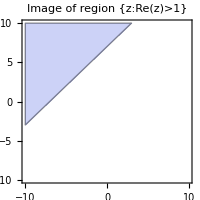

```mathematica
A1=RegionPlot[Re[z]>1,{x,-10,10},{y,-10,10},Axes->True,ImageSize->200,
PlotLabel->"Region{z:Re(z)>1}"];
A2=RegionPlot[Re[1/2(-5+I(1-z)-z)]>1,{x,-10,10},{y,-10,10},Axes->True,ImageSize->200,
PlotLabel->"Image of region {z:Re(z)>1}"];
Print[A1,A2]
```

# PRACTICAL-6

Show that the image of the right half plane A={z:Re z>=1/2 under the mapping w=f(z)=1/z is the closed disk D_1(1)={w:|w-1|≤1} in the w-plane.

```mathematica
Quit[]
```

```mathematica
Solve[w1==1/z1,z1]
```

{{z1→1/w1}}

```mathematica
z=x+I y;
```

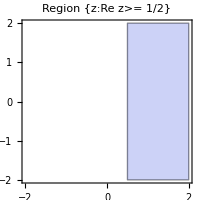
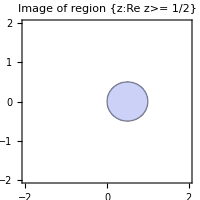

```mathematica
A1=RegionPlot[Re[z]>0.5,{x,-2,2},{y,-2,2},Axes->True,ImageSize->200,PlotLabel->"Region {z:Re z>= 1/2}"];
A2=RegionPlot[Re[1/z]>1,{x,-2,2},{y,-2,2},Axes->True,ImageSize->200,PlotLabel->"Image of region {z:Re z>= 1/2}"];
Print[A1,A2]
```

# PRACTICAL-7

Make a plot of the vertical lines x=a, for a=-1,-1/2,1/2,1 and the horizontal lines, y=b for b=-1,-1/2,1/2,1. Find the plot of this grid under the mapping w=f(z)=1/z.

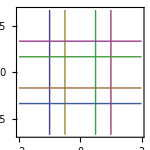
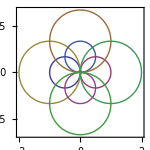

```mathematica
z=x+I y;
A1=ContourPlot[{Re[z]==-1,Re[z]==1,Re[z]==-1/2,Re[z]==1/2,Im[z]==-1,Im[z]==1,Im[z]==-1/2,Im[z]==1/2},{x,-2,2},{y,-2,2},Axes->True,ImageSize->150];
A2=ContourPlot[{Re[1/z]==-1,Re[1/z]==1,Re[1/z]==-1/2,Re[1/z]==1/2,Im[1/z]==-1,Im[1/z]==1,Im[1/z]==-1/2,Im[1/z]==1/2},{x,-2,2},{y,-2,2},Axes->True,ImageSize->150];
Print[A1,A2]
```

# PRACTICAL-8

Find a parametrization of the polygon path C=C1+C2+C3 from -1+i to 3+i, where C_1 is the line from:-1+i to -1, C_2 is the line from:-1 to 1+i and C_3 is the line from 1+i to 3-i. Make a plot of this path.

Parametric Plot of polygon path c (t) = C_1(t) + C_2(t)+C_3(t)

```mathematica
Quit[]
```

```mathematica
Subscript[C, 1][t_]=ComplexExpand[(-1+I)*(1-t)+(-1)*t];
Subscript[C, 2][t_]=ComplexExpand[(-1)*(1-t)+(1+I)*t];
Subscript[C, 3][t_]=ComplexExpand[(1+I)*(1-t)+(3-I)*t];
```

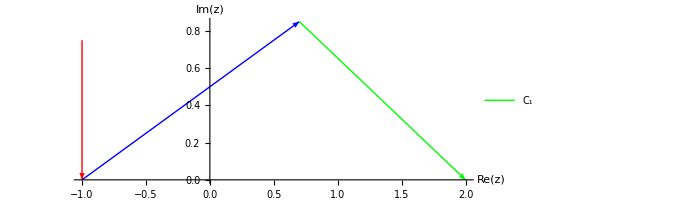

```mathematica
Show[ParametricPlot[{ReIm[Subscript[C, 1][t]],ReIm[Subscript[C, 2][t]],ReIm[Subscript[C, 3][t]]},{t,0,1},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},PlotLegends->{"C_1","C_2","C_3"},AxesLabel->{"Re(z)","Im(z)"}],
Graphics[{Red,Arrow[{{-1,0.75},{-1,0}}]}],
Graphics[{Blue,Arrow[{{-1,0},{0.7,0.85}}]}],
Graphics[{Green,Arrow[{{0.7,0.85},{2,0}}]}],PlotRange->2]
```

# PRACTICAL-9

Plot the line segment ‘L’ joining the point A=0 to B=2+π/4i and give an exact calculation of ∫_L e^z ⅆz

```mathematica
Integrate[e^z,{z,0,2+π/4 I}]
```

(-1+e^(2+(ⅈ π)/4))/Log[e]

Some other examples: Find ∫_(2+3i)^(5+2i) z^2 ⅆz, ∫_(2+3i)^(5+2i) e^z ⅆz, ∫_0^(2+i) z̄ ⅆz, ∫_-2^(-2+i) (z+2)^2 ⅆz.

```mathematica
Print["The value of intergral ∫_(2 + 3  i)^(5 + 2  i) z^2ⅆz is : ",Integrate[z^2,{z,2+3I,5+2I}]]
```

The value of intergral ∫_(2 + 3  i)^(5 + 2  i) z^2ⅆz is : 37+(133 ⅈ)/3

```mathematica
Print["The value of intergral ∫_(2 + 3  i)^(5 + 2  i) e^zⅆz is : ",Integrate[e^z,{z,2+3I,5+2I}]]
```

The value of intergral ∫_(2 + 3  i)^(5 + 2  i) e^zⅆz is : (-e^(2+3 ⅈ)+e^(5+2 ⅈ))/Log[e]

# PRACTICAL-10

Plot the semicircle ‘C’ with radius 1 centered at z=2 and evaluate the contour integral ∫_C 1/(z-2)ⅆz

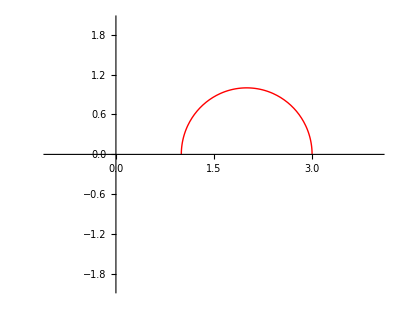

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,Pi},
PlotRange->{{-1,4},{-2,2}},PlotStyle->{Red,Thick},ImageSize->{250}]
```

```mathematica
Quit[]
```

```mathematica
f[z_]:=1/(z-2);
z[t_]:=2+Cos[t]+I Sin[t];
∫_0^π f[z[t]]z'[t]ⅆt
```

ⅈ π

Some other examples: ∫_C 1/z ⅆz where c is a circle with centre at origin and radius r

```mathematica
f[z_]:=1/z;
z[t_]:=r Cos[t]+I r Sin[t];
∫_0^(2π) f[z[t]]z'[t]ⅆt
```

2 ⅈ π

Evaluate∫_C (z-i)ⅆz where C is a parabola y=x^2 : -1<= x<= 1

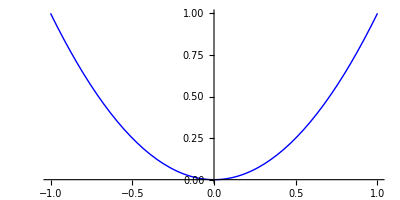

```mathematica
ParametricPlot[{t,t^2},{t,-1,1},PlotStyle->{Red,Blue},ImageSize->{250}]
```

```mathematica
f[z_]:=z-I;
z[t_]:=t+I t^2;
∫_-1^1 f[z[t]]z'[t]ⅆt
```

0

# PRACTICAL-11

Show that ∫_C zⅆz  =∫_C zⅆz  =4+2i where C_1 is the line segment from -1-i to 3+i and C_2 is the portion of the parabola x=y^2+2y joining from -1-i to 3+i. Make plot of two contours C_1,C_2 joining -1-i to 3+i

```mathematica
Integrate[z,{z,-1-I,3+I}]
```

4+2 ⅈ

```mathematica
f[z_]:=z;
z[t_]:=(t^2+2t)+I t;
∫_-1^1 f[z[t]]z'[t]ⅆt
```

4+2 ⅈ

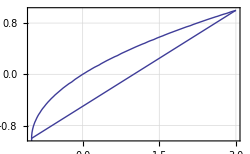

```mathematica
A1=ListLinePlot[{{Re[-1-I],Im[-1-I]},{Re[3+I],Im[3+I]}},
ImageSize->250,GridLines->Automatic,Frame->True];
A2=ContourPlot[{x==y^2+2y},{x,-2,3},{y,-3,3},Axes->{True,True},GridLines->Automatic,ImageSize->150,Frame->True,PlotLabel->"Graph of x==y^2+2y"];
Show[A1,A2]
```

# PRACTICAL-12

Use ML inequality to show that |∫_C 1/(z^2+1)ⅆz| <= 1/(2 √5)where C is the straight line segment from 2+2i while solving represent the distance from the point z to the point i and -i i.e, |z-i| & |z+i| in the complex plane.

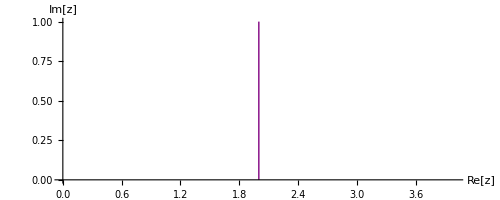

```mathematica
f[z_]:=1/(z^2+1)
z[t_]:=2+I*t
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->Purple,Axes->True,AxesLabel->{"Re[z]","Im[z]"}]
```

The length of the curve,L is given by

```mathematica
Integrate[Abs[z'[t]],{t,0,1}]
```

1

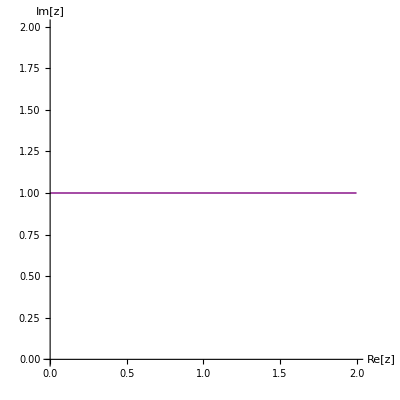

```mathematica
z[t_]:=2*(1-t)+I
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->Purple,Axes->True,AxesLabel->{"Re[z]","Im[z]"}]
```

Again the distance |z+i| i.e the distance from z to -i least when z=2

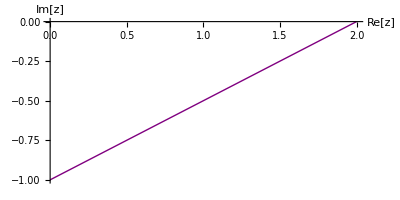

```mathematica
z[t_]:=2(1-t)-I*t
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->Purple,Axes->True,AxesLabel->{"Re[z]","Im[z]"}]
```

```mathematica
g[t_]=4+(4+6I)t
```

4+(4+6 ⅈ) t

# PRACTICAL-13

Find and plot three different Laurent series representation for the function f(z)=3/(2+z-z^2)involving powers of z

```mathematica
Grid[Table[{n,Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}],Frame->All]
```

0 | 3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+(513 z^8)/512-(1023 z^9)/1024+(2049 z^10)/2048
2 | 1/3+(2-z)/9-1/(-2+z)+1/27 (-2+z)^2-1/81 (-2+z)^3+1/243 (-2+z)^4-1/729 (-2+z)^5+(-2+z)^6/2187-(-2+z)^7/6561+(-2+z)^8/19683-(-2+z)^9/59049+(-2+z)^10/177147
∞ | -513/z^10-255/z^9-129/z^8-63/z^7-33/z^6-15/z^5-9/z^4-3/z^3-3/z^2

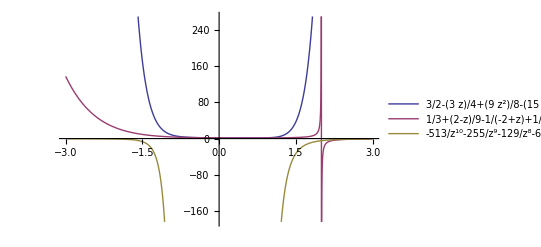

```mathematica
Plot[Evaluate[Table[{Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}]],{z,-3,3},PlotLegends->"Expressions"]
```

# PRACTICAL-14

Locate the poles of f(z)=1/(5 z^4+26 z^2+5).

```mathematica
f[z_]:=1/(5z^4+26z^2+5);
Print["f[z]=",f[z]];
Print[Denominator[f[z]]==0];
solset=Sort[Solve[Denominator[f[z]]==0,z]];
Print[solset];
Print["The singularities are"];
z1=ReplaceAll[z,solset[[1]]];
Print["z1=",z1];
z2=ReplaceAll[z,solset[[2]]];
Print["z2=",z2]
z3=ReplaceAll[z,solset[[3]]];
Print["z3=",z3];
z4=ReplaceAll[z,solset[[4]]];
Print["z4=",z4];
```

f[z]=1/(5+26 z^2+5 z^4)

5+26 z^2+5 z^4==0

{{z→-ⅈ/(√5)},{z→ⅈ/(√5)},{z→-ⅈ √5},{z→ⅈ √5}}

The singularities are

z1=-ⅈ/(√5)

z2=ⅈ/(√5)

z3=-ⅈ √5

z4=ⅈ √5

# PRACTICAL-15

Locate the zeroes and poles of g(z)=πCot[πz]/z^2. Determine their order, also justify that Res(g,0)=-π^2/3.

```mathematica
g[z_]:=π*Cot[π*z]/z^2;
Reduce[g[z]==0,z]
```

C[1]∈Integers&&z≠0&&z==(π/2+π C[1])/π

```mathematica
Poles=Solve[Denominator[g[z]]==0,z]
```

{{z→0},{z→0}}

```mathematica
residue=Residue[g[z],{z,0}]
```

-π^2/3

# PRACTICAL-16

Evaluate ∫_((C^+)_(1(0))) e^(2/z)ⅆz  where C_1^+(0) denotes the circle{z : |z|=1} with positive orientation. Similarly evaluate ∫_(C_1^+(0)) 1/(z^4+z^3-2 z^2)ⅆx

```mathematica
Quit[]
```

```mathematica
f[z_]:=Exp[2/z]
g[t_]:=Cos[t]+I*Sin[t]
∫_0^(2π) f[g[t]]*g'[t]ⅆt
```

4 ⅈ π

```mathematica
h[z_]:=1/z^4+z^3-2z^2
g[t_]:=Cos[t]+I*Sin[t]
∫_0^(2π) h[g[t]]*g'[t]ⅆt
```

0